## definitions

After a renormalization step, a given site i of the n^th approximant becomes either molecular (in which case n becomes n-2) or atomic (n becomes n-3). 
We can thus associate to each site a unique “renormalization path”: the sequence of molecular/atomic sites that has led to it, starting from the trivial (F_n=1) chain and inflating it.

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
ClearAll[i,n];
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]
```

In the limit ρ->0 fractal dimensions no longer depend on the site i, but only on the relative time spent on molecular sites, which we shall call x.
Letting n_m be the number of molecular renormalizations and n_a be the number of atomic renormalization, we have
x = n_m/(n_m+n_a)∈ [0, 1/2]

```mathematica
(* false when n<3 *)
test=#[[3]]≥3&;
(* take a site (i), a size (n) and return the renormalization path for this site *)
path[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]->i
(* variant where we forget about the site number *)
path2[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]
(* compute the relative time spent on molecular sites (x) *)
xPath[i_,n_]:={i,StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]/n}
(* variant where we forget about the site number *)
xPath2[i_,n_]:=StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]/n
```

```mathematica
(* generate the whole (x) tree! *)
tree[n_]:=xPath[#,n]&/@ Range[Fibonacci[n]]
(* variant where we forget about the site number, and compute nx rather than x *)
tree2[n_]:=Sort[n xPath2[#,n]&/@ Range[Fibonacci[n]]]
```

```mathematica
(* Display all the paths for a system size *)
paths[n_]:=path2[#,n]&/@Range[Fibonacci[n]]
```

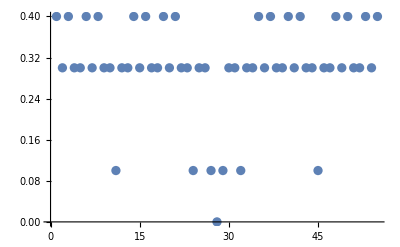

```mathematica
(* wow, such tree, much xs! *)
ListPlot[tree[10],Joined->False]
```

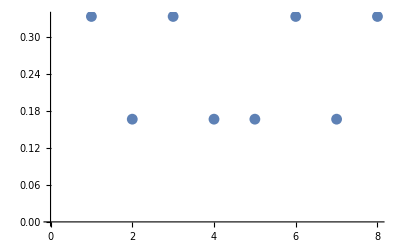

```mathematica
(* wow, such tree, much xs! *)
ListPlot[tree[6],Joined->False]
```

```mathematica
m=3;
n=3*m+1;
n*Sort@DeleteDuplicates[Transpose[tree[n]]//Last]
```

{0,1,3,4}

```mathematica
m=4;
l=m-0;
Tally[tree2[3m+1]]
Print["Take a("<>ToString[l]<>")=",a[l]];
2^a[l]((a[l]+m-l)!)/((m-l)!(a[l])!)
```

{{0,1},{1,8},{3,80},{4,80},{6,64}}

Take a(4)=6

64

```mathematica
((a[l]+m-l)!)/((m-l)!(a[l])!)
```

5

```mathematica
a[3]
```

4

```mathematica
m=4;
Tally[paths[3m+1]];
Sort[%,#1[[2]]>#2[[2]]&]
```

{{mmmmmm,64},{mmmma,16},{mmmam,16},{mmamm,16},{mammm,16},{ammmm,16},{mmmaa,8},{mmama,8},{mamma,8},{ammma,8},{mmaam,8},{mamam,8},{ammam,8},{maamm,8},{amamm,8},{aammm,8},{maaa,2},{amaa,2},{aama,2},{aaam,2},{aaaa,1}}

```mathematica
Limit[2^a[nn]/Fibonacci[3nn +1],nn->Infinity]
```

0

```mathematica
m=3;
Tally[tree2[3m+2]]
2^b[m]
```

{{0,1},{2,24},{3,32},{5,32}}

32

```mathematica
(* n = 3m +1 case *)
a[m_]:=3+(m-2)3/2+(-1)^m/4-1/4
(* n = 3m +2 case *)
b[m_]:=3+(m-2)3/2-(-1)^m/4+1/4
```

```mathematica
a[4]
```

6

```mathematica
(* list all possible values of x *)
7*Sort@DeleteDuplicates[Transpose[tree[7]]//Last]
10*Sort@DeleteDuplicates[Transpose[tree[10]]//Last]
13*Sort@DeleteDuplicates[Transpose[tree[13]]//Last]
16*Sort@DeleteDuplicates[Transpose[tree[16]]//Last]
22*Sort@DeleteDuplicates[Transpose[tree[22]]//Last]
```

{0,1,3}

{0,1,3,4}

{0,1,3,4,6}

{0,1,3,4,6,7}

{0,1,3,4,6,7,9,10}

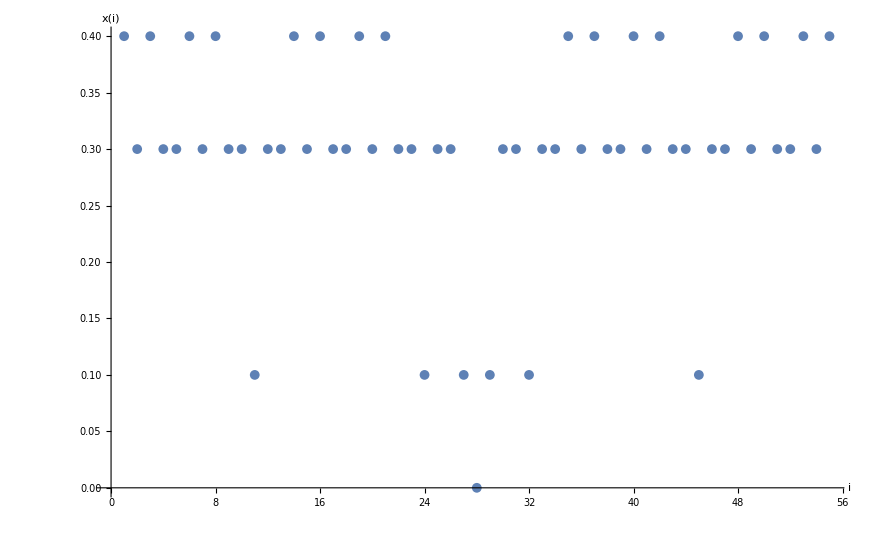

```mathematica
l=tree[10];
m=Max[l];
ListPlot[l,PlotRange->All,PlotStyle->PointSize[.008],Joined->True,ColorFunction->Function[{x,y},ColorData["ThermometerColors"][y ]],AxesLabel->{"i","x(i)"}]/.Line->Point
(*Export[dir<>"data/local_dim_wf_rho_20.png",%,ImageResolution->200]*)
```

```mathematica
Position[tree[10],4/10];
Transpose[%]//First
```

{1,3,6,8,14,16,19,21,35,37,40,42,48,50,53,55}

## Application

### Energy/co-label representation

```mathematica
n=10;

(* compute x for each site *)
xlist=tree[n];
(* drop the site labels, they are unecessary as x is indexed by increasing x label *)
xlist=Last@(Transpose[xlist]);
(* list all possible values of x *)
xvalues=Sort@DeleteDuplicates[xlist];
(* list all positions by increasing value of x *)
listPos=Flatten[Position[xlist,#]]&/@xvalues;

(* intensities by increasing value of x *)
intx=Range[Length[xvalues]];
(* intensity table *)
int=Table[0,{it,Fibonacci[n]}];
MapThread[(int[[#1]]=#2)&,{listPos,intx}];

mask=Table[int[[i]]int[[j]],{i,Fibonacci[n]},{j,Fibonacci[n]}];
```

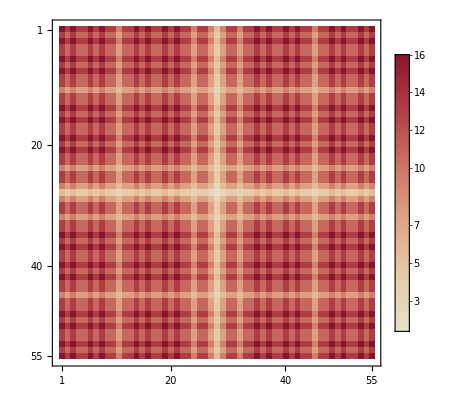

```mathematica
MatrixPlot[mask,ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

### Labelling energy states

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
n=8;
(* permutation rule reordering sites by increasing x label *)
perm=Ordering@Transpose[tree[n+2]][[2]];

(* wavefunctions in the co-basis, ordered by increasing x label *)
wf=Block[{val,vec,i=n,ts=10.,tw=1.},
{val,vec}=Eigensystem[hp[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering@val]];
vec=vec[[perm]];
Transpose[Transpose[vec][[perm]]]
];
```

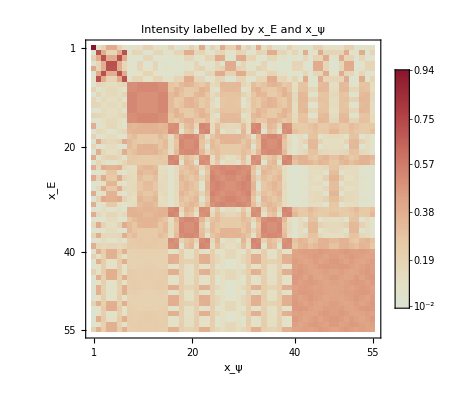

```mathematica
MatrixPlot [Abs[wf]^2,FrameLabel->{"x_E","x_ψ"},PlotLabel->"Intensity labelled by x_E and x_ψ",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```